```mathematica
g[t_,u_,v_, h_, m_]:=t/2.*m^2+u*m^4+v*m^6-h*m
```

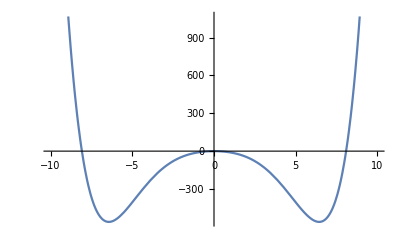

Plot3D::plld: Endpoints for t in {t,-1.,-1.} must have distinct machine-precision numerical values.

Plot3D[g[t,-0.5,0.1,1.5,m],{t,-1.,-1.},{m,-10.,10.}]

```mathematica
Plot[g[-20., -0.5,0.01,0.0,m],{m,-10.,10.}]
Plot3D[g[t,-0.5,0.1, 1.5, m], {t, -1.0, -1.0}, {m,-10.,10.}]
```

```mathematica
Manipulate[Plot[g[20.*t/100, 0.5*u/100,0.02*v/100,20.0*h/100,m],{m,-10.,10.}],{t,-100,100},{u,-100,100},{v,50,100}, {h,-100,100}]
```